```mathematica
n=({{"", "收藏", "播放", "分享", "评论", "弹幕", "硬币", "当前排名", "历史排名"}, {1, 2, 3, 4, 5, 6, 7, 8, 9}});
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
dat=Import["bili.csv"];
```

```mathematica
l=Dimensions@dat
```

{945,9}

```mathematica
(* dat⟦All,1⟧=TimeZoneConvert[Interpreter["DateTime"][dat⟦#,1⟧],8]&/@Range@l⟦1⟧; 这个太慢了 *)
```

```mathematica
$TimeZone=2; (* 从法国时区转换 *)
```

```mathematica
dat⟦All,1⟧=TimeZoneConvert[
DateObject@AbsoluteTime[{dat⟦#,1⟧,{"Year","/","Month","/","Day"," ","Hour24",":","Minute"}}],8]&/@Range@l⟦1⟧;
```

```mathematica
$TimeZone=8;
```

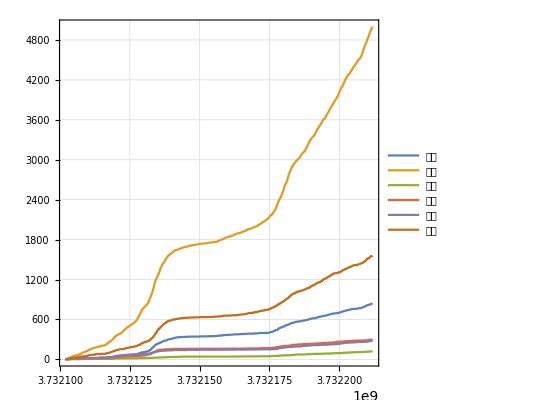

```mathematica
u=l⟦1⟧;
DateListPlot[dat⟦1;;u,{1,#+1}⟧&/@Range@6,PlotRange->{{dat⟦1,1⟧,dat⟦u,1⟧},All},PlotLegends->n⟦1,2;;7⟧,GridLines->Automatic,GridLinesStyle->Directive[Gray,Thin, Dashed],AspectRatio->1]
```